----------------------------------------------------------------------------------

----------------------------------Output is below---------------------------------

--------------------Shock parameters before and behind shock----------------------

Pressure before the shock

1/4 (4 pL+rhoL uL^2+rhoL uL^2 γ-√rhoL uL √(16 pL γ+rhoL uL^2 (1+γ)^2))

Density before the shock

(rhoL (4 pL γ+rhoL uL^2 (1+γ)-√rhoL uL √(16 pL γ+rhoL uL^2 (1+γ)^2)))/(2 rhoL uL^2 (-1+γ)+4 pL γ)

Shock speed before reflection

(-√rhoL uL (-3+γ)+√(16 pL γ+rhoL uL^2 (1+γ)^2))/(4 √rhoL)

----------------------------------------------------------------------------------

Numerical values

Pressure behind shock:		 1
Density behind shock:		  1
Velocity behind shock:		 1.5

Pressure before shock:		 0.12009

Density before shock:		  0.28113

Velocity before shock:		 0

Shock speed before reflection: 2.08661

----------------------------------------------------------------------------------

Checking Rankine-Hugoniot conditions

Mass flux condition:		True
Momentum flux condition:	True
Energy flux condition:	  True

----------------------------------------------------------------------------------

--------------------Shock parameters after shock reflection-----------------------

Pressure after shock reflection

1/4 (4 pL+rhoL uL^2+rhoL uL^2 γ+√rhoL uL √(16 pL γ+rhoL uL^2 (1+γ)^2))

Density after shock reflection

(rhoL (4 pL γ+rhoL uL^2 (1+γ)+√rhoL uL √(16 pL γ+rhoL uL^2 (1+γ)^2)))/(2 rhoL uL^2 (-1+γ)+4 pL γ)

Shock speed after rzeflection

(√rhoL uL (-3+γ)+√(16 pL γ+rhoL uL^2 (1+γ)^2))/(4 √rhoL)

----------------------------------------------------------------------------------

Numerical values after shock refletion

Pressure:	4.57991

Density:	 2.69184

Shock speed: 0.886607

----------------------------------------------------------------------------------

Checking Rankine-Hugoniot conditions after shock reflection

Mass flux condition:		True
Momentum flux condition:	True
Energy flux condition:	  True

----------------------------------------------------------------------------------

Shock reflection schematics

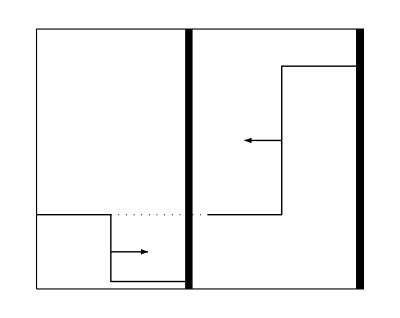

```mathematica
ClearAll["Global`*"]
eq1=rhoL*(S1-uL)==rhoR*S1;eq2=rhoL*(S1-uL)^2+pL==rhoR*S1^2+pR;eq3=(S1-uL)^2/2+γ/(γ-1)*pL/rhoL==S1^2/2+γ/(γ-1)*pR/rhoR;
eq4=rhoL*(uL+S2)==rhoRR*S2;eq5=rhoL*(uL+S2)^2+pL==rhoRR*S2^2+pRR;eq6=(uL+S2)^2/2+γ/(γ- 1)*pL/rhoL==S2^2/2+γ/(γ-1)*pRR/rhoRR;
sol1=Simplify[Solve[eq1 &&eq2&&eq3 ,{rhoR,pR,S1}]];sol2=Simplify[Solve[eq4 && eq5 && eq6,{rhoRR,pRR,S2}]]; 
pR=pR /. sol1; rhoR = rhoR /. sol1; S1=S1 /. sol1;
pRR=pRR /. sol2; rhoRR=rhoRR /.sol2; S2=S2 /. sol2;
Style["----------------------------------------------------------------------------------",15,Red,Bold]
Style["----------------------------------Output is below---------------------------------",15,Red,Bold]
Style["--------------------Shock parameters before and behind shock----------------------",15,Red,Bold]
Style["Pressure before the shock",15,Red,Bold]
pR=pR [[2]]
Style["Density before the shock",15,Red,Bold]
rhoR=rhoR[[2]]
Style["Shock speed before reflection",15,Red,Bold]
S1=S1[[2]]
pLN = 1; uLN = 1.5;rhoLN = 1; 
Style["----------------------------------------------------------------------------------",15,Red,Bold]
Style["Numerical values", 15, Red, Bold]
Print["Pressure behind shock:\t\t ",Style[pLN, 15, Blue, Bold], "\nDensity behind shock:\t\t  ",Style[rhoLN, 15, Blue, Bold],"\nVelocity behind shock:\t\t ",Style[uLN,15,Blue,Bold]]
Print["Pressure before shock:\t\t ",Style[pRN=pR /. {rhoL->rhoLN,uL->uLN,pL->pLN,γ->1.4},15, Red, Bold]]
Print["Density before shock:\t\t  ",Style[rhoRN=rhoR /. {rhoL->rhoLN,uL->uLN,pL->pLN,uR->uRN,γ->1.4},15,Red,Bold]]
Print["Velocity before shock:\t\t ",Style[0,15,Blue,Bold]]
Print["Shock speed before reflection: ",Style[SNB=S1 /. {rhoL->rhoLN,uL->uLN,pL->pLN,uR->uRN,γ->1.4},15,Red,Bold]]
Style["----------------------------------------------------------------------------------",15,Red,Bold]
Print[Style["Checking Rankine-Hugoniot conditions",15,Red,Bold]]
cont=(rhoLN*(SNB-uLN)==rhoRN*SNB);momentum=(rhoLN*(SNB-uLN)^2+pLN==rhoRN*SNB^2+pRN/. γ->1.4);
energy=((SNB-uLN)^2/2+γ/(γ-1)*pLN/rhoLN==SNB^2/2+γ/(γ-1)*pRN/rhoRN /. γ->1.4);
t1="Mass flux condition:\t\t"; t1c=Style[cont,If[cont,Green,Red],Bold];
t2="Momentum flux condition:\t"; t2c=Style[momentum,If[momentum,Green,Red],Bold];
t3="Energy flux condition:\t  "; t3c=Style[energy,If[energy,Green,Red],Bold];
Print[t1,t1c,"\n",t2,t2c,"\n",t3,t3c]
Style["----------------------------------------------------------------------------------",15,Red,Bold]
Style["--------------------Shock parameters after shock reflection-----------------------",15,Red,Bold]
Style["Pressure after shock reflection", 15, Red, Bold]
pRR=pRR[[2]]
Style["Density after shock reflection", 15, Red, Bold]
rhoRR=rhoRR[[2]]
Style["Shock speed after rzeflection", 15, Red, Bold]
S2=S2[[2]]
Style["----------------------------------------------------------------------------------",15,Red,Bold]
Style["Numerical values after shock refletion", 15, Red, Bold]
Print["Pressure:\t",Style[pRRN=pRR /. {rhoL->rhoLN,uL->uLN,pL->pLN,γ->1.4},15,Red,Bold]]
Print["Density:\t ",Style[rhoRRN=rhoRR /. {rhoL->rhoLN,uL->uLN,pL->pLN,γ->1.4},15,Red,Bold]]
Print["Shock speed: ",Style[SNA=S2 /. {rhoL->rhoLN,uL->uLN,pL->pLN,γ->1.4},15,Red,Bold]]
Style["----------------------------------------------------------------------------------",15,Red,Bold]
Style["Checking Rankine-Hugoniot conditions after shock reflection", 15, Red, Bold]
cont = (rhoLN*(uLN+SNA)==rhoRRN*SNA) ;momentum = (rhoLN*(uLN+SNA)^2+pLN==rhoRRN*SNA^2+pRRN/.γ->1.4);
energy = ((uLN+SNA)^2/2+γ/(γ-1)*pLN/rhoLN==SNA^2/2+γ/(γ-1)*pRRN/rhoRRN /. γ->1.4);
t1="Mass flux condition:\t\t"; t1c=Style[cont,If[cont,Green,Red],Bold];
t2="Momentum flux condition:\t"; t2c=Style[momentum,If[momentum,Green,Red],Bold];
t3="Energy flux condition:\t  "; t3c=Style[energy,If[energy,Green,Red],Bold];
Print[t1,t1c,"\n",t2,t2c,"\n",t3,t3c]
Style["----------------------------------------------------------------------------------",15,Red,Bold]
Style["Shock reflection schematics", 15, Red, Bold]
l1 = Line[{{0,1},{1,1},{1,0.1},{2,0.1}}];l2=Line[{{2.3,1},{3.3,1},{3.3,3},{4.3,3}}];
l3={Dotted,Line[{{1,1},{2,1}}]}; l4={Dotted,Line[{{2.1,1},{2.3,1}}]};
a1=Arrow[{{1,0.5},{1.5,0.5}}];a2=Arrow[{{3.3,2},{2.8,2}}];r1=Rectangle[{2,0},{2.1,3.5}];r2=Rectangle[{4.3,0},{4.4,3.5}];
r3={EdgeForm[Black],FaceForm[],Rectangle[{0,0},{4.4,3.5}]};Graphics[{l1,l2,l3,l4,a1,a2,r1,r2,r3}]
```